# Quorum Sensing in V. Fischeri

## Introducing the system of Differential Equations

```mathematica
Acoord[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_] = k2 C1 - k1 A R - n (A - Aex) + p (f C1)/(1+f C1)
```

C1 k2-(A-Aex) n+(C1 f p)/(1+C1 f)-A k1 R

```mathematica
Rcoord[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_] = k2 C1 - k1 A R - b (R) + q (f C1)/(1+f C1)
```

C1 k2+(C1 f q)/(1+C1 f)-b R-A k1 R

```mathematica
C1coord[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_] =  k1 A R -k2 C1
```

-C1 k2+A k1 R

## Equilibrium States

```mathematica
sol = Simplify[Solve [{k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t])  == 0 , k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ==0, k1 A[t] R[t] -k2 C1[t] ==0},{A[t],R[t],C1[t]}]]
```

{{A[t]→Aex,R[t]→0,C1[t]→0},{A[t]→1/2 (Aex+p/n+(f √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(√(-f^3) √k1 n √q)),R[t]→(-Aex f^2 √k1 n q+f^2 √k1 p q-√(-f^3) √q √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(2 b f^2 √k1 p),C1[t]→(-2 b f k2 n+Aex f^2 k1 n q+f^2 k1 p q-√(-f^3) √k1 √q √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(2 b f^2 k2 n)},{A[t]→1/2 (Aex+p/n+(√(-f^3) √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(f^2 √k1 n √q)),R[t]→(-Aex f^2 √k1 n q+f^2 √k1 p q+√(-f^3) √q √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(2 b f^2 √k1 p),C1[t]→(-2 b f k2 n+Aex f^2 k1 n q+f^2 k1 p q+√(-f^3) √k1 √q √(4 b k2 n p-f k1 (Aex n+p)^2 q))/(2 b f^2 k2 n)}}

```mathematica
Reduce[{4 b k2 n p-f k1 (Aex n+p)^2 q<0, Aex>0,k1>0,k2>0,n>0,b>0,p>0,q>0,f>0},f]
```

p>0&&n>0&&Aex>0&&q>0&&k2>0&&k1>0&&b>0&&f>(4 b k2 n p)/(Aex^2 k1 n^2 q+2 Aex k1 n p q+k1 p^2 q)

```mathematica
FullSimplify[(4 b k2 n p)/(Aex^2 k1 n^2 q+2 Aex k1 n p q+k1 p^2 q)]
```

(4 b k2 n p)/(k1 (Aex n+p)^2 q)

```mathematica
Reduce[{4 b k2 n p-f k1 (Aex n+p)^2 q<0, Aex==0,k1>0,k2>0,n>0,b>0,p>0,q>0,f>0},f]
```

q>0&&p>0&&n>0&&k2>0&&k1>0&&b>0&&Aex==0&&f>(4 b k2 n)/(k1 p q)

```mathematica
(*WANT  f>(4 b k2 n)/(k1 p q) for S1 and S2 to exist*)
```

## Figure 2 - Schematic of Steady states

```mathematica
parVal={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1};
parValA = {k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex-> 0};
```

```mathematica
eqlbrm =  sol/.parVal
```

{{A[t]→Aex,R[t]→0,C1[t]→0},{A[t]→1/2 (3+Aex-1/100 ⅈ √(36000-100 (30+10 Aex)^2)),R[t]→(300 √5-100 √5 Aex-ⅈ √5 √(36000-100 (30+10 Aex)^2))/(360 √5),C1[t]→1/600 (2400+1000 Aex-10 ⅈ √(36000-100 (30+10 Aex)^2))},{A[t]→1/2 (3+Aex+1/100 ⅈ √(36000-100 (30+10 Aex)^2)),R[t]→(300 √5-100 √5 Aex+ⅈ √5 √(36000-100 (30+10 Aex)^2))/(360 √5),C1[t]→1/600 (2400+1000 Aex+10 ⅈ √(36000-100 (30+10 Aex)^2))}}

```mathematica
eqlbrmNoAex =N[eqlbrm/.Aex-> 0//Values]
```

{{0.,0.,0.},{2.6619,1.47883,7.87298},{0.338105,0.187836,0.127017}}

```mathematica
eqlbrmNoAex[[1]]
```

{0.,0.,0.}

```mathematica
GMan = Manipulate [ssn = sol/.parVal;
Eqpts = N[ssn/.Aex->extA//Values]; 
ListPointPlot3D[Eqpts],{{extA,0,"Aex"},0,20} ]
```

```mathematica
ssn1 = Sort[N[sol/.parValA//Values]];
```

```mathematica
Show[ListPointPlot3D[ssn1, AxesLabel->{A,R,C}],Graphics3D@Line@ssn1, Graphics3D[{Text["(*Graphics3DBox[GraphicsComplex3DBox[NCache[{{0, 0, (Rational[9, 8] + Rational[3, 8] 5^Rational[1, 2])^Rational[1, 2]}, {0, 0, Rational[-1, 2] (Rational[3, 2] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-3 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[-1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (3 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {-(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], (Rational[1, 8] + Rational[1, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[-1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {(Rational[3, 4] + Rational[1, 3] 5^Rational[1, 2])^Rational[1, 2], Rational[1, 2], Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {-(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {(Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], 0, (Rational[5, 8] + Rational[5, 24] 5^Rational[1, 2])^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (-1 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Rational[-1, 2] (Rational[5, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2], Rational[1, 4] (1 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (-3 - 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}, {Root[1 - 36 #^2 + 144 #^4& , 2, 0], Rational[1, 4] (3 + 5^Rational[1, 2]), Rational[-1, 2] (Rational[1, 6] (3 + 5^Rational[1, 2]))^Rational[1, 2]}}, {{0, 0, 1.4012585384440737`}, {0, 0, -1.4012585384440737`}, {0.17841104488654497`, -1.3090169943749475`, 0.46708617948135783`}, {0.17841104488654497`, 1.3090169943749475`, 0.46708617948135783`}, {0.46708617948135783`, -0.8090169943749475, -1.0444364486709836`}, {0.46708617948135783`, 0.8090169943749475, -1.0444364486709836`}, {1.0444364486709836`, -0.8090169943749475, 0.46708617948135783`}, {1.0444364486709836`, 0.8090169943749475, 0.46708617948135783`}, {-1.2228474935575286`, -0.5, 0.46708617948135783`}, {-1.2228474935575286`, 0.5, 0.46708617948135783`}, {1.2228474935575286`, -0.5, -0.46708617948135783`}, {1.2228474935575286`, 0.5, -0.46708617948135783`}, {-0.9341723589627157, 0, -1.0444364486709836`}, {-0.46708617948135783`, -0.8090169943749475, 1.0444364486709836`}, {-0.46708617948135783`, 0.8090169943749475, 1.0444364486709836`}, {0.9341723589627157, 0, 1.0444364486709836`}, {-1.0444364486709836`, -0.8090169943749475, -0.46708617948135783`}, {-1.0444364486709836`, 0.8090169943749475, -0.46708617948135783`}, {-0.17841104488654494`, -1.3090169943749475`, -0.46708617948135783`}, {-0.17841104488654494`, 1.3090169943749475`, -0.46708617948135783`}}], Polygon3DBox[{{15, 10, 9, 14, 1}, {2, 6, 12, 11, 5}, {5, 11, 7, 3, 19}, {11, 12, 8, 16, 7}, {12, 6, 20, 4, 8}, {6, 2, 13, 18, 20}, {2, 5, 19, 17, 13}, {4, 20, 18, 10, 15}, {18, 13, 17, 9, 10}, {17, 19, 3, 14, 9}, {3, 7, 16, 1, 14}, {16, 8, 4, 15, 1}}]],Boxed->False,ImageSize->30,ViewPoint->{1.3, -2.4, 2.},ViewVertical->{0., 0., 1.}])",ssn1[[1]]]}], Graphics3D[{Text["",ssn1[[2]]]}],Graphics3D[{Text["",ssn1[[3]]]}], Graphics3D[{Text["Stable Steady State S2",{3.3,1,9}]}],Graphics3D[{Text["Unstable Steady State S1",{1.2,0.2,0.3}] }],Graphics3D[{Text["Stable steady state S0 = (Aex,0,0)",{-1,0,0}] }]]
```

-Graphics3D-

## Jacobian Stuff

```mathematica
JacobianMatrixGen[p_,func_,var_]:= Outer[D,Simplify[Through[Apply[func, Join[var,p]]]],var]
```

```mathematica
genJ=JacobianMatrixGen[{Aex,k1,k2,n,b,p,q,f},{Acoord, Rcoord,C1coord},{A,R,C1}] //MatrixForm
```

(-n-k1 R | -A k1 | k2-(C1 f^2 p)/(1+C1 f)^2+(f p)/(1+C1 f)
-k1 R | -b-A k1 | k2-(C1 f^2 q)/(1+C1 f)^2+(f q)/(1+C1 f)
k1 R | A k1 | -k2)

```mathematica
jacobM =FullSimplify[genJ]
```

(-n-k1 R | -A k1 | k2+(f p)/(1+C1 f)^2
-k1 R | -b-A k1 | k2+(f q)/(1+C1 f)^2
k1 R | A k1 | -k2)

## Eigen Stuff

### General

```mathematica
jacobM  =FullSimplify[ JacobianMatrixGen[{Aex,k1,k2,n,b,p,q,f},{Acoord, Rcoord,C1coord},{A,R,C1}]]
```

{{-n-k1 R,-A k1,k2+(f p)/(1+C1 f)^2},{-k1 R,-b-A k1,k2+(f q)/(1+C1 f)^2},{k1 R,A k1,-k2}}

```mathematica
jacobParam =jacobM/.parValA
```

{{-10-20 R,-20 A,10+30/(1+C1)^2},{-20 R,-3-20 A,10+5/(1+C1)^2},{20 R,20 A,-10}}

```mathematica
solNoT = Simplify[Solve [{Acoord[A,R,C1,Aex,k1,k2,n,b,p,q,f]  == 0 ,Rcoord[A,R,C1,Aex,k1,k2,n,b,p,q,f]  ==0, C1coord[A,R,C1,Aex,k1,k2,n,b,p,q,f]==0},{A,R,C1}]];
```

```mathematica
solNoT[[1]]
```

{A→Aex,R→0,C1→0}

### Stability of S0

```mathematica
jacobS0=jacobM/.solNoT[[1]]
```

{{-n,-Aex k1,k2+f p},{0,-b-Aex k1,k2+f q},{0,Aex k1,-k2}}

```mathematica
ES0 = Eigenvalues[jacobS0]
```

{-n,1/2 (-b-Aex k1-k2-√((b+Aex k1+k2)^2-4 (b k2-Aex f k1 q))),1/2 (-b-Aex k1-k2+√((b+Aex k1+k2)^2-4 (b k2-Aex f k1 q)))}

```mathematica
(*ALWAYS NEGATIVE : JUSTIFICATION :  - (Pos Stuff) +/- (Something smaller than Pos Stuff) < 0 *)
```

```mathematica
jacobParamS0 = Eigenvalues[jacobS0/.parValA]
```

{-10,-10,-3}

```mathematica
(* With given parameters, we get always stable S0 as expected *)
```

### Stability of S1

```mathematica
jacobS1=jacobM/.solNoT[[3]];
```

```mathematica
jacobParamS1 = N[Eigenvalues[jacobS1/.parValA]]
```

{-28.9789,-5.89921,1.35932}

```mathematica
(*NOT STABLE in the regime of given parameter values*)
```

### Stability of S2

```mathematica
jacobS2=jacobM/.solNoT[[2]];
```

```mathematica
jacobParamS2 = N[Eigenvalues[jacobS2/.parValA]]
```

{-98.0192,-7.47826,-0.317019}

```mathematica
(*STABLE in the regime of given parameter values*)
```

## Running Simulations - Single Trajectories

### Single Trajectory

#### S1 !!!

```mathematica
parValA={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 };
```

```mathematica
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == 0.02, R[0]==  0.05, C1[0] ==0.15}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
```

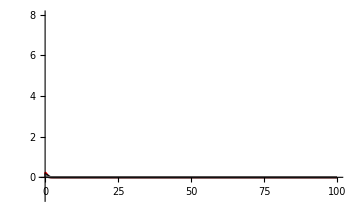

```mathematica
Plot[Evaluate [{A[t],R[t],C1[t]}/. syst],{t,0.001,100}, PlotRange->{{0,100},{-1,8}}, PlotStyle->{Red,Black, Gray}]
```

```mathematica
Manipulate[mansys =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] ==Ainit, R[0]==  Rinit, C1[0] ==C1init}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
Plot[Evaluate [{A[t],R[t],C1[t]}/. mansys],{t,0.001,20}, PlotRange->{{0,20},{-1,8}}, PlotStyle->{Red,Black, Gray}],{Ainit,0,0.5},{Rinit,0,0.5},{C1init,0,0.5}]
```

```mathematica
syst/.t-> 15
```

{{A[15]→-2.89542×10^-13,R[15]→7.36581×10^-12,C1[15]→2.82325×10^-15}}

```mathematica
val15 = syst/.t->15[[]]//Values
```

{{-2.89542×10^-13,7.36581×10^-12,2.82325×10^-15}}

```mathematica
Eqpt = Nearest[eqlbrmNoAex,val15][[1]]
```

{{0.,0.,0.}}

```mathematica
dist = EuclideanDistance[val15,Eqpt]
```

7.3715×10^-12

### Single Trajectory

#### S2 !!!

```mathematica
parValA={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 };
```

```mathematica
Manipulate[mansys =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] ==Ainit, R[0]==  Rinit, C1[0] ==C1init}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
Plot[Evaluate [{A[t],R[t],C1[t]}/. mansys],{t,0.001,20}, PlotRange->{{0,20},{0,10}}, PlotStyle->{Red,Black, Gray}],{Ainit,1.75,3.75},{Rinit,0.5,2.5},{C1init,6.75,8.75}]
```

```mathematica
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == 2.5, R[0]==  0.7, C1[0] ==7.5}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
```

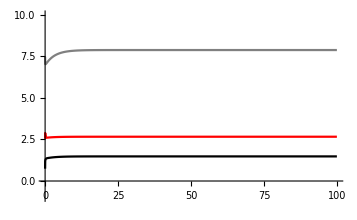

```mathematica
Plot[Evaluate [{A[t],R[t],C1[t]}/. syst],{t,0.001,100}, PlotRange->{{0,100},{-1,10}}, PlotStyle->{Red,Black, Gray}]
```

#### In terms of Speed

```mathematica
time = Range[1,100,0.2];
```

```mathematica
syst/.t-> #&/@time;
```

```mathematica
val100 = syst/.t-> #&/@time//Values;
```

```mathematica
funcSpeed[vals_] := Through[Apply[{Acoord,Rcoord,C1coord}, Join[vals[[1]],{Aex, k1,k2,n, b,p,q,f} ]]]/.parValA
```

```mathematica
speed100 = funcSpeed[#]&/@val100;
```

```mathematica
speed100;
```

```mathematica
speedNorm =Norm[#]&/@speed100;
```

```mathematica
speedNorm;
```

```mathematica
time[[FirstPosition[speedNorm,_?(#<10^-5&)][[1]]]]
```

32.6

```mathematica
N[funcSpeed[{{2.75,1.5,7.75}}]]
```

{-5.92857,-5.07143,5.}

## Figure 3 - Stability of S2

### Figure 3

```mathematica
(*Defining a function that inputs values of (A,R,C) and estimates the speed of approach to equilibrium by plugging in (A,R,C) into ODE system*)
```

```mathematica
funcSpeed[vals_] := Through[Apply[{Acoord,Rcoord,C1coord}, Join[vals[[1]],{Aex, k1,k2,n, b,p,q,f} ]]]/.parValA
```

```mathematica
(*Defining a function that inputs initial condition and generates time to reach eqlbm*)
```

```mathematica
functionIC2timeEq[in_] := Module[{parValA,eqlbrm,syst,val100,speed100 ,speedNorm, time},
parValA={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 };
eqlbrm =  N[sol/.parValA//Values];
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == in[[1]], R[0]==  in[[2]], C1[0] ==in[[3]]}/. parValA,{A[t],R[t], C1[t]},{t,0.01,100}, MaxSteps->10000];
time = N[Range[100]];

	syst/.t-> #&/@Range[100];
	val100 = syst/.t-> #&/@Range[100]//Values;
	speed100 = funcSpeed[#]&/@val100;
	speedNorm =Norm[#]&/@speed100;
	getEqTime =time[[FirstPosition[speedNorm,_?(#<10^-3&)][[1]]]]
(*The threshold is chosen such that the white shading appears when time to eqlbrm  ~15 sec, see color legend below*)
]
```

```mathematica
S2sphere = Sphere[eqlbrmNoAex[[2]]]
```

Sphere[{2.6619,1.47883,7.87298}]

```mathematica
s2pts = RandomPoint[S2sphere, 1000];
```

```mathematica
timeforS2 = functionIC2timeEq[#]&/@s2pts;
```

```mathematica
x2 = s2pts[[All,1]];
y2 = s2pts[[All,2]];
z2=s2pts[[All,3]];
```

```mathematica
n2 =timeforS2;
```

```mathematica
n2;
```

```mathematica
pairs = Transpose[{x2,y2,z2,n2}];
```

```mathematica
colorfunc=Interpolation[{{#1,#2,#3},#4}&@@@Transpose[{x2,y2,z2,n2}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ListSurfacePlot3D[Transpose[{x2,y2,z2}],ColorFunction->(ColorData[{"GrayTones",MinMax@n2}][colorfunc[#1,#2,#3]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData[{"GrayTones",MinMax@n2}],{0,30}}],AxesLabel->{A,R,C1}]
```

-Graphics3D-

## Figure 4 - Instability of S1

```mathematica
(*Defining a function that inputs initial condition and generates time to reach eqlbm*)
```

```mathematica
functionIC2timeEq2[in_] := Module[{parValA,eqlbrm,syst,val100,speed100 ,speedNorm, time},
parValA={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 };
eqlbrm =  N[sol/.parValA//Values];
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == in[[1]], R[0]==  in[[2]], C1[0] ==in[[3]]}/. parValA,{A[t],R[t], C1[t]},{t,0.01,100}, MaxSteps->10000];
time = N[Range[100]];

	syst/.t-> #&/@Range[100];
	val100 = syst/.t-> #&/@Range[100]//Values;
	speed100 = funcSpeed[#]&/@val100;
	speedNorm =Norm[#]&/@speed100;
	getEqTime =time[[FirstPosition[speedNorm,_?(#<10^-1.32&)][[1]]]] 
(*The threshold is chosen such that the white shading appears when time to eqlbrm  ~15 sec, see color legend below*)
]
```

```mathematica
S1sphere = Sphere[eqlbrmNoAex[[3]],0.1]
```

Sphere[{0.338105,0.187836,0.127017},0.1]

```mathematica
s1pts = RandomPoint[S1sphere, 1000];
```

```mathematica
timeforS1 = functionIC2timeEq2[#]&/@s1pts;
```

```mathematica
x1= s1pts[[All,1]];
y1 = s1pts[[All,2]];
z1=s1pts[[All,3]];
```

```mathematica
n1 =timeforS1;
```

```mathematica
pairs = Transpose[{x1,y1,z1,n1}];
```

```mathematica
colorfunc=Interpolation[{{#1,#2,#3},#4}&@@@Transpose[{x1,y1,z1,n1}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ListSurfacePlot3D[Transpose[{x1,y1,z1}],ColorFunction->(ColorData[{"GrayTones",MinMax@n1}][colorfunc[#1,#2,#3]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData[{"GrayTones",MinMax@n1}],{0,30}}],AxesLabel->{A,R,C1}]
```

-Graphics3D-

#### Confirming Black is S0 and White is S1

```mathematica
functionIC2whichS[in_] := Module[{parValA,eqlbrm,syst,val15,Eqpt ,speedNorm, time},
parValA={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 };
eqlbrm =  N[sol/.parValA//Values];
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == in[[1]], R[0]==  in[[2]], C1[0] ==in[[3]]}/. parValA,{A[t],R[t], C1[t]},{t,0.01,20}, MaxSteps->10000];
	val15 = syst/.t->15[[]]//Values;
	Eqpt = Nearest[eqlbrm,val15][[1,1]];
	If[Eqpt == eqlbrm[[1]],graysc = 0, graysc = 20 ] 
]
```

```mathematica
whichS = functionIC2whichS[#]&/@s1pts;
```

```mathematica
nS=whichS;
```

```mathematica
pairs = Transpose[{x1,y1,z1,nS}];
```

```mathematica
colorfunc=Interpolation[{{#1,#2,#3},#4}&@@@Transpose[{x1,y1,z1,nS}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ListSurfacePlot3D[Transpose[{x1,y1,z1}],ColorFunction->(ColorData[{"GrayTones",MinMax@n1}][colorfunc[#1,#2,#3]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData[{"GrayTones",MinMax@n1}],{0,30}}],AxesLabel->{A,R,C1}]
```

-Graphics3D-

```mathematica
(*THIS Fig is very similar (at least qualitatively in first sight) to Fig 4. Hence it shows that in Fig 4, black DOES correspond to state S0 and white DOES correspond to state S2 *)
```

```mathematica
(*This thus confirms our hypothesis that there is an on-off switch event without Aex that is controlled by the parameters and the initial conditions of the system!!!!)
```

## Figure 5 - Quorum Sensing in Action

```mathematica
xaxis = Range[100];
```

```mathematica
yax = xaxis/(1+n*Aex/p)^2/.parVal;
```

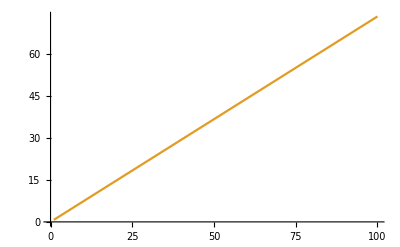

```mathematica
ListLinePlot[Transpose[{xaxis,yax}]/.{parVal,{Aex-> 0.5}}]
```

```mathematica
Manipulate[xaxis = Range[100];
yaxis = xaxis/(1+n*Aex/p)^2/.parVal;
ListLinePlot[Transpose[{xaxis,yaxis}]/.parVal, PlotRange-> {{1,100},{1,100}}],{Aex,0,1}]
```

```mathematica
Manipulate[RegionPlot[(y>x/(1+n*Aex/p)^2)/.parVal,{x,0,100},{y,0,100}],{Aex,0,1} ]
```

```mathematica
Manipulate[xaxis = Range[100];
yaxis = xaxis/(1+n*Aex/p)^2/.parVal;
Show[ ListLinePlot[Transpose[{xaxis,yaxis}], PlotRange-> {{1,100},{1,100}}   ],   RegionPlot[(y>x/(1+n*Aex/p)^2)/.parVal,{x,0,100},{y,0,100}  ]],{Aex,0,1}]
```

```mathematica
ListLinePlot[Transpose[{xaxis,yax}]/.{parVal,{Aex-> 0.5}}]
```

-Graphics-

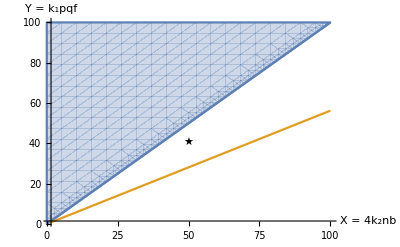

```mathematica
Show[ListLinePlot[Transpose[{xaxis,yaxis}], PlotRange-> {{1,100},{1,100}} , AxesLabel->{"X = 4k_2nb", "Y = k_1pqf"}  ],   RegionPlot[(y>x/(1+n*Aex/p)^2)/.parValA,{x,0,100},{y,0,100} ] , ListLinePlot[Transpose[{xaxis,yax}]/.{parVal,{Aex-> 1}}], Graphics[{Text["★", {50,40}]}]  ]
```

## Extension - Attacking LuxR using Halogenated Furanones

```mathematica
ADrug[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_,eps_] = k2 C1 - k1 A R - n (A - Aex) + p (f C1)/(1+f C1)
```

C1 k2-(A-Aex) n+(C1 f p)/(1+C1 f)-A k1 R

```mathematica
RDrug[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_, eps_] = k2 C1 - k1 A R - b (R) +( 1-eps) q (f C1)/(1+f C1)
```

C1 k2+(C1 (1-eps) f q)/(1+C1 f)-b R-A k1 R

```mathematica
C1Drug[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_,eps_] =  k1 A R -k2 C1
```

-C1 k2+A k1 R

```mathematica
solNoT = Simplify[Solve [{ADrug[A,R,C1,Aex,k1,k2,n,b,p,q,f,eps]  == 0 ,RDrug[A,R,C1,Aex,k1,k2,n,b,p,q,f, eps]  ==0, C1Drug[A,R,C1,Aex,k1,k2,n,b,p,q,f,eps]==0},{A,R,C1}]];
```

```mathematica
quick =solNoT/.parValA ;
```

```mathematica
quick/. eps->0
```

{{A→0,R→0,C1→0},{A→-1/200 ⅈ (300 ⅈ+60 ⅈ √15),R→(30 √3+30 √5)/(36 √5),C1→1/600 (2400+600 √15)},{A→1/2 (3-3 √(3/5)),R→(-30 √3+30 √5)/(36 √5),C1→1/600 (2400-600 √15)}}

```mathematica
Simplify[quick[[2]]]
```

{A→3/10 (5+(√5 √(-3+5 eps))/(√(-1+eps))),R→1/6 (5-5 eps-√5 √(-1+eps) √(-3+5 eps)),C1→4-5 eps-√5 √(-1+eps) √(-3+5 eps)}

```mathematica
solDrug1 =(Simplify[quick[[2]]]//Values)[[3]]
```

4-5 eps-√5 √(-1+eps) √(-3+5 eps)

```mathematica
Manipulate[mansys =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + (1-eps) q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] ==Ainit, R[0]==  Rinit, C1[0] ==C1init}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
Plot[Evaluate [{A[t],R[t],C1[t]}/. mansys],{t,0.001,20}, PlotRange->{{0,20},{0,10}}, PlotStyle->{Red,Black, Gray}],{Ainit,0,5},{Rinit,0,4},{C1init,0,9}, {eps,0,0.6}]
```

```mathematica
(*Solving the new system*)
```

```mathematica
soleps = Simplify[Solve [{ADrug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]  == 0 ,RDrug[A,R,C1,Aex,k1,k2,n,b,p,q,f, epss]  ==0, C1Drug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]==0},{A,R,C1}]]
```

{{A→Aex,R→0,C1→0},{A→1/2 (Aex+(√(-1+epss) √f √k1 p √q+√(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(√(-1+epss) √f √k1 n √q)),R→(√q ((-1+epss) (Aex n-p) √q-(√(-1+epss) √(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(√f √k1)))/(2 b p),C1→-(2 b k2 n-Aex f k1 n q+Aex epss f k1 n q-f k1 p q+epss f k1 p q+√(-1+epss) √f √k1 √q √(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(2 b f k2 n)},{A→1/2 (Aex+(epss p)/((-1+epss) n)+p/(n-epss n)-(√(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(√(-1+epss) √f √k1 n √q)),R→(√q ((-1+epss) (Aex n-p) √q+(√(-1+epss) √(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(√f √k1)))/(2 b p),C1→(-2 b k2 n+Aex f k1 n q-Aex epss f k1 n q+f k1 p q-epss f k1 p q+√(-1+epss) √f √k1 √q √(4 b k2 n p+(-1+epss) f k1 (Aex n+p)^2 q))/(2 b f k2 n)}}

```mathematica
quickeps = soleps/.parValA
```

{{A→0,R→0,C1→0},{A→(√(36000+90000 (-1+epss))+300 √(-1+epss))/(200 √(-1+epss)),R→(-(√(36000+90000 (-1+epss)) √(-1+epss))/(2 √5)-30 √5 (-1+epss))/(36 √5),C1→1/600 (2400-10 √(36000+90000 (-1+epss)) √(-1+epss)-3000 epss)},{A→1/2 (30/(10-10 epss)-(√(36000+90000 (-1+epss)))/(100 √(-1+epss))+(3 epss)/(-1+epss)),R→((√(36000+90000 (-1+epss)) √(-1+epss))/(2 √5)-30 √5 (-1+epss))/(36 √5),C1→1/600 (2400+10 √(36000+90000 (-1+epss)) √(-1+epss)-3000 epss)}}

```mathematica
Solve[√(36000+90000 (-1+epss))==0, epss]
```

{{epss→3/5}}

```mathematica
(* Seeing the bifurcation with Eps, bifurcation point eps = 0.6, or 3/5 *)
```

```mathematica
Manipulate[  
soleps = Simplify[Solve [{ADrug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]  == 0 ,RDrug[A,R,C1,Aex,k1,k2,n,b,p,q,f, epss]  ==0, C1Drug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]==0},{A,R,C1}]];
quickeps = soleps/.parValA/.epss->eps;
jacobeps  =N[FullSimplify[ JacobianMatrixGen[{Aex,k1,k2,n,b,p,q,f,eps},{ADrug, RDrug,C1Drug},{A,R,C1}]]/.parValA/.quickeps];
Eigenvalues/@jacobeps, {eps,0,1}]
```

```mathematica
Manipulate[  
soleps = Simplify[Solve [{ADrug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]  == 0 ,RDrug[A,R,C1,Aex,k1,k2,n,b,p,q,f, epss]  ==0, C1Drug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]==0},{A,R,C1}]];
quickeps = N[soleps/.parValA/.epss->eps] //Values, {eps,0,1}]
```

```mathematica
(* epss = 3/5 is the cutoff point *)
```

```mathematica
Manipulate[  
soleps = Simplify[Solve [{ADrug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]  == 0 ,RDrug[A,R,C1,Aex,k1,k2,n,b,p,q,f, epss]  ==0, C1Drug[A,R,C1,Aex,k1,k2,n,b,p,q,f,epss]==0},{A,R,C1}]];
quickeps = N[soleps/.parValA/.epss->eps] //Values;
CeqVal = quickeps[[2,3]];
ListPlot[{ Re[CeqVal]}, PlotRange->All]
, {eps,0,0.6}]
```

```mathematica
xvalues={0.0,0.6,1.2,2.4,4.9,9.8,19.5,39.1}
yvalues1={50,35,30,25,20,10,5,0}
yvalues2={80,68,55,40,35,20,7,0}
```

{0.,0.6,1.2,2.4,4.9,9.8,19.5,39.1}

{50,35,30,25,20,10,5,0}

{80,68,55,40,35,20,7,0}

```mathematica
newxvec = Rescale[xvalues]*0.6
```

{0.,0.00920716,0.0184143,0.0368286,0.0751918,0.150384,0.299233,0.6}

```mathematica
newy1 =  Rescale[yvalues1]
newy2 = Rescale[yvalues2]
```

{1,7/10,3/5,1/2,2/5,1/5,1/10,0}

{1,17/20,11/16,1/2,7/16,1/4,7/80,0}

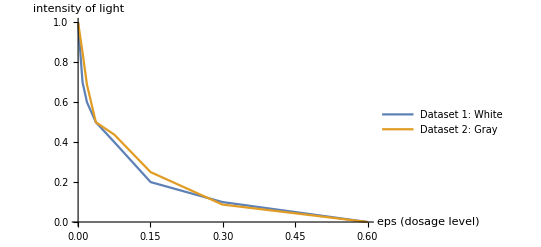

```mathematica
Plot1 = ListPlot[{Transpose[{newxvec,newy1}], Transpose[{newxvec, newy2}]}, Joined->True, PlotLegends->{"Dataset 1: White","Dataset 2: Gray"}, AxesLabel->{"eps (dosage level)","intensity of light"}]
```

```mathematica
model=a Exp[- k x]
```

{a ⅇ^-k,a ⅇ^(-4 k)}

```mathematica
Fit1 = FindFit[Transpose[{xvalues,yvalues1}],model,{a,k},x]
```

General::ivar: 1 is not a valid variable.

FindFit[{{0.,50},{0.6,35},{1.2,30},{2.4,25},{4.9,20},{9.8,10},{19.5,5},{39.1,0}},{a ⅇ^-k,a ⅇ^(-4 k)},{a,k},{1,4}]

```mathematica
Fit1 = FindFit[Transpose[{xvalues,yvalues2}],model,{a,k},x]
```

General::ivar: 1 is not a valid variable.

FindFit[{{0.,80},{0.6,68},{1.2,55},{2.4,40},{4.9,35},{9.8,20},{19.5,7},{39.1,0}},{a ⅇ^-k,a ⅇ^(-4 k)},{a,k},{1,4}]

```mathematica
solDrug1
```

4-5 eps-√5 √(-1+eps) √(-3+5 eps)

```mathematica
N[4-5 eps-√5 √(-1+eps) √(-3+5 eps)/.eps->0]
```

7.87298

```mathematica
(*Normalization Factor for 'C' *)
```

```mathematica
Exp[7.872983346207417]
```

2625.39

```mathematica
(*Normalization Factor for 'Exp[C]' *)
```

```mathematica
Simplify[f solDrug1/ (1+ f solDrug1)/. parValA]
```

(-4+5 eps+√5 √(-1+eps) √(-3+5 eps))/(-5+5 eps+√5 √(-1+eps) √(-3+5 eps))

```mathematica
N[(-4+5 eps+√5 √(-1+eps) √(-3+5 eps))/(-5+5 eps+√5 √(-1+eps) √(-3+5 eps))/.eps->0]
```

0.887298

```mathematica
(*Normalization Factor for 'fC/(1+fC)' *)
```

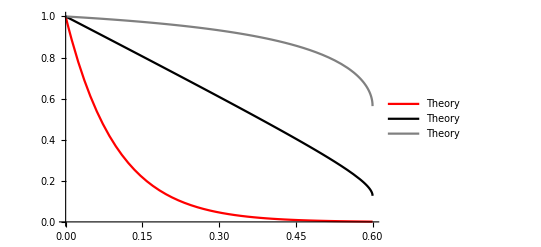

```mathematica
Plot2 = Plot[{Exp[solDrug1]/2625.386352781244,solDrug1/7.872983346207417, f solDrug1/ (0.8872983346207418*(1+ f solDrug1))/. parValA},{eps,0,0.6},PlotStyle->{Red,Black, Gray}, PlotLegends->{"Theory","Theory","Theory" }]
```

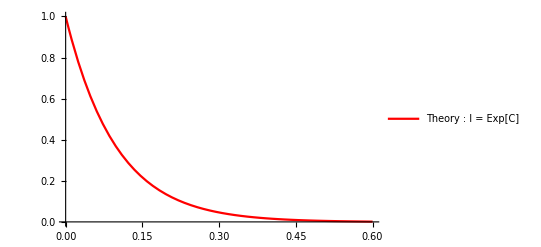

```mathematica
Plot3 =  Plot[ Exp[solDrug1]/2625.386352781244,{eps,0,0.6},PlotStyle->Red,PlotLegends->{"Theory : I = Exp[C]"}]
```

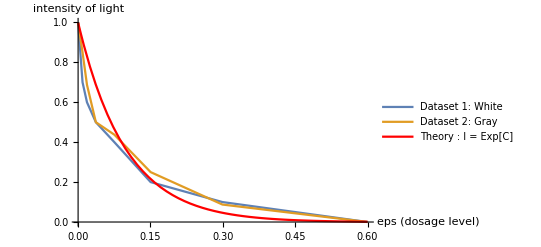

```mathematica
Show[Plot1, Plot3]
```

## Extension - Optimal Combination of Drugs

```mathematica
ADrugComb[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_,epsR_, epsA_] = k2 C1 - k1 A R - n (A - Aex) + (1-epsA)p (f C1)/(1+f C1)
```

C1 k2-(A-Aex) n+(C1 (1-epsA) f p)/(1+C1 f)-A k1 R

```mathematica
RDrugComb[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_, epsR_, epsA_] = k2 C1 - k1 A R - b (R) +( 1-epsR) q (f C1)/(1+f C1)
```

C1 k2+(C1 (1-epsR) f q)/(1+C1 f)-b R-A k1 R

```mathematica
C1DrugComb[A_,R_,C1_, Aex_, k1_,k2_,n_, b_,p_,q_,f_, epsR_, epsA_] =  k1 A R -k2 C1
```

-C1 k2+A k1 R

```mathematica
Manipulate[mansys =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + (1-epsA)p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + (1-epsR) q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] ==Ainit, R[0]==  Rinit, C1[0] ==C1init}/. parValA,{A[t],R[t], C1[t]},{t,0.001,100}, MaxSteps->10000];
Plot[Evaluate [{A[t],R[t],C1[t]}/. mansys],{t,0.001,20}, PlotRange->{{0,20},{0,10}}, PlotStyle->{Red,Black, Gray}],{Ainit,0,5},{Rinit,0,4},{C1init,0,9}, {epsR,0,1},{epsA, 0,1} ]
```

```mathematica
solNoT2 = Simplify[Solve [{ADrugComb[A,R,C1,Aex,k1,k2,n,b,p,q,f,epsR, epsA]  == 0 ,RDrugComb[A,R,C1,Aex,k1,k2,n,b,p,q,f, epsR, epsA]  ==0, C1DrugComb[A,R,C1,Aex,k1,k2,n,b,p,q,f,epsR, epsA]==0},{A,R,C1}]];
```

```mathematica
quick2=Simplify[solNoT2/.parValA ];
```

```mathematica
N[quick2/. {epsR->0, epsA->0}];
```

```mathematica
Simplify[quick2[[3]]];
```

```mathematica
solDrug2 =(Simplify[quick2[[3]]]//Values)[[3]]
```

4+5 epsA (-1+epsR)+√5 √((-1+epsA) (3+5 epsA (-1+epsR)-5 epsR) (-1+epsR))-5 epsR

```mathematica
solDrug2/. {epsR->0, epsA->0}
```

4+√15

```mathematica
Plot3D[solDrug2,{epsR,0,1},{epsA,0,1}, AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Minimize[{solDrug2, 0.4≥ epsR≥ 0,  0.4≥ epsA≥ 0}, {epsR, epsA}]
```

NMinimize::nrnum: The function value -3.15685+0.537684 ⅈ is not a real number at {epsA,epsR} = {0.389312,0.39637}.

{1.59341,{epsA→0.367448,epsR→0.332703}}

```mathematica
(*Comparison to ONLY 1 drug epsR*)
```

```mathematica
4-5 eps-√5 √(-1+eps) √(-3+5 eps)/.eps->0.33270293562179337
```

4.44816+0. ⅈ

```mathematica
(* 1.59 vs 4.45 -> reduced to 30 percent *)
```

## Extension - Stability of S2 in the presence of the drug

```mathematica
(*Defining a function that inputs values of (A,R,C) and estimates the speed of approach to equilibrium by plugging in (A,R,C) into ODE system*)
```

```mathematica
funcSpeedDrug[vals_] := Through[Apply[{ADrug,RDrug,C1Drug}, Join[vals[[1]],{Aex, k1,k2,n, b,p,q,f,eps} ]]]/.parValA
```

```mathematica
(*Defining a function that inputs initial condition and generates time to reach eqlbm*)
```

```mathematica
functionDRUGtimeEq[in_] := Module[{parValAeps,,syst,val100,speed100 ,speedNorm, time},
parValAeps={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 , eps-> 0.4};(* <<<---- WE CHANGE EPS HERE*)
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + (1-eps)q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == in[[1]], R[0]==  in[[2]], C1[0] ==in[[3]]}/. parValAeps,{A[t],R[t], C1[t]},{t,0.01,100}, MaxSteps->10000];
time = N[Range[100]];

	syst/.t-> #&/@Range[100];
	val100 = syst/.t-> #&/@Range[100]//Values;
	speed100 = funcSpeedDrug[#]&/@val100/. parValAeps;
	speedNorm =Norm[#]&/@speed100;
	getEqTime =time[[FirstPosition[speedNorm,_?(#<10^-5&)][[1]]]]
(*The threshold is chosen such that the white shading appears when time to eqlbrm  ~15 sec, see color legend below*)
]
```

```mathematica
neweqDrug = Re[N[((solNoT/. parValA)//Values)/. eps-> 0.4]]
```

{{0.,0.,0.},{2.36603,0.788675,3.73205},{0.633975,0.211325,0.267949}}

```mathematica
S2sphere = Sphere[neweqDrug[[2]]]
```

Sphere[{2.36603,0.788675,3.73205}]

```mathematica
s2pts = RandomPoint[S2sphere, 500];
```

```mathematica
s2pts[[1,1]]
```

2.587

```mathematica
timeforS2 = functionDRUGtimeEq[#]&/@s2pts;
```

```mathematica
x2 = s2pts[[All,1]];
y2 = s2pts[[All,2]];
z2=s2pts[[All,3]];
```

```mathematica
n2 =timeforS2;
```

```mathematica
n2;
```

```mathematica
pairs = Transpose[{x2,y2,z2,n2}];
```

```mathematica
colorfunc=Interpolation[{{#1,#2,#3},#4}&@@@Transpose[{x2,y2,z2,n2}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ListSurfacePlot3D[Transpose[{x2,y2,z2}],ColorFunction->(ColorData[{"GrayTones",MinMax@n2}][colorfunc[#1,#2,#3]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData[{"GrayTones",MinMax@n2}],{0,30}}],AxesLabel->{A,R,C1}]
```

-Graphics3D-

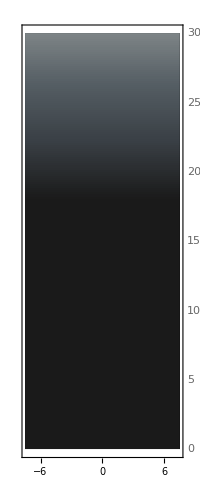
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D-

```mathematica
-Graphics3D--Graphics3D--Graphics3D--Graphics3D-
```

(a) eps = 0				    (b) eps = 0.2				     (c) eps = 0.4 			    (d) eps = 0.55

## Extension - INStability of S1 in the presence of the drug

```mathematica
funcSpeedDrug[vals_] := Through[Apply[{ADrug,RDrug,C1Drug}, Join[vals[[1]],{Aex, k1,k2,n, b,p,q,f,eps} ]]]/.parValA
```

```mathematica
(*Defining a function that inputs initial condition and generates time to reach eqlbm*)
```

```mathematica
functionDRUGtimeEq[in_] := Module[{parValAeps,,syst,val100,speed100 ,speedNorm, time},
parValAeps={k1 -> 20, k2-> 10, n-> 10, b-> 3, p -> 30, q -> 5, f-> 1, Aex ->  0 , eps-> 0.55}; (* <<<---- WE CHANGE EPS HERE*)
syst =NDSolve[{A'[t]== k2 C1[t] - k1 A[t] R[t] - n (A[t] - Aex) + p (f C1[t])/(1+f C1[t]) ,
R'[t] == k2 C1[t] - k1 A[t] R[t] - b (R[t]) + (1-eps)q (f C1[t])/(1+f C1[t])  ,
C1'[t] == k1 A[t] R[t] -k2 C1[t] ,
A[0] == in[[1]], R[0]==  in[[2]], C1[0] ==in[[3]]}/. parValAeps,{A[t],R[t], C1[t]},{t,0.01,100}, MaxSteps->10000];
time = N[Range[100]];

	syst/.t-> #&/@Range[100];
	val100 = syst/.t-> #&/@Range[100]//Values;
	speed100 = funcSpeedDrug[#]&/@val100/. parValAeps;
	speedNorm =Norm[#]&/@speed100;
	getEqTime =time[[FirstPosition[speedNorm,_?(#<10^-5&)][[1]]]]
(*The threshold is chosen such that the white shading appears when time to eqlbrm  ~15 sec, see color legend below*)
]
```

```mathematica
neweqDrug = Re[N[((solNoT/. parValA)//Values)/. eps-> 0.55]]
```

{{0.,0.,0.},{2.,0.5,2.},{1.,0.25,0.5}}

```mathematica
S2sphere = Sphere[ neweqDrug[[3]],0.1]
```

Sphere[{1.,0.25,0.5},0.1]

```mathematica
s2pts = RandomPoint[S2sphere, 500];
```

```mathematica
s2pts[[1,1]]
```

1.08417

```mathematica
timeforS2 = functionDRUGtimeEq[#]&/@s2pts;
```

```mathematica
x2 = s2pts[[All,1]];
y2 = s2pts[[All,2]];
z2=s2pts[[All,3]];
```

```mathematica
n2 =timeforS2;
```

```mathematica
n2;
```

```mathematica
pairs = Transpose[{x2,y2,z2,n2}];
```

```mathematica
colorfunc=Interpolation[{{#1,#2,#3},#4}&@@@Transpose[{x2,y2,z2,n2}],InterpolationOrder->1]
```

InterpolatingFunction[…]

-Graphics3D-

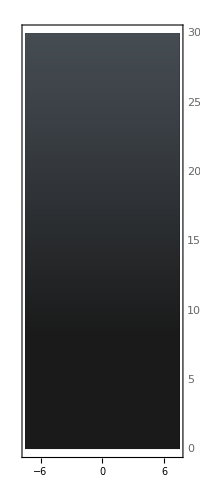
-Graphics- -Graphics3D- -Graphics3D- -Graphics3D- -Graphics3D-

```mathematica
ListSurfacePlot3D[Transpose[{x2,y2,z2}],ColorFunction->(ColorData[{"GrayTones",MinMax@n2}][colorfunc[#1,#2,#3]]&),ColorFunctionScaling->False,PlotLegends->BarLegend[{ColorData[{"GrayTones",MinMax@n2}],{0,30}}],AxesLabel->{A,R,C1}]
```

(a) eps = 0				    (b) eps = 0.2				     (c) eps = 0.4 			    (d) eps = 0.55